```mathematica
Quiet@Map[SetOptions[#,BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->Black,Frame->True,Axes->None,FrameTicksStyle->Black,FrameStyle->Directive[Black,Thickness[0.004]],Method->{"TransparentPolygonMesh"->True}]&,InputForm[Symbol/@Names["System`*Plot"]]];
logticksx=Join[{Log10@#,Switch[#,10^-1,0.1,1,1,10,10,_,Superscript[10,Log10@#]],{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
logticksx2=Join[{Log10@#,"",{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
Msunt = ToString[Subscript["M","⊙"],FormatType->StandardForm];
```

```mathematica
hmf = ReadList[NotebookDirectory[]<>"hmf.dat",Table[Number,{5}]];
hmfi = Interpolation[{#[[1]],#[[2]],#[[3]]}&/@hmf];
dotMi = Interpolation[{#[[1]],#[[2]],#[[4]]}&/@hmf];
DdotMi = Interpolation[{#[[1]],#[[2]],#[[5]]}&/@hmf,InterpolationOrder->1];
```

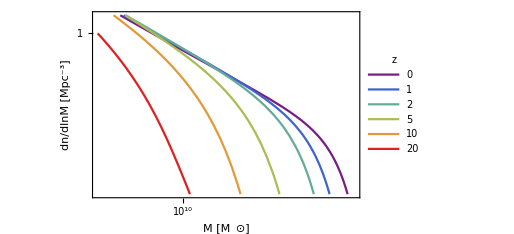

```mathematica
Plot[Log10[10^9hmfi[#,10^logM]]&/@{0.01,1,2,5,10,20}//Evaluate,{logM,7,Log10@hmfi[[1,2,2]]},FrameLabel->{"M ["<>Msunt<>"]","dn/dlnM [Mpc^-3]"},PlotRange->{{7,16},{-9,1}},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,5]),ImageSize->380,PlotRangePadding->None,FrameTicks->{{logticksx,logticksx2},{logticksx,logticksx2}},PlotLegends->LineLegend[Automatic,{0,1,2,5,10,20},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendMarkerSize->{10,4},LegendLabel->Style["z",14]]]
```

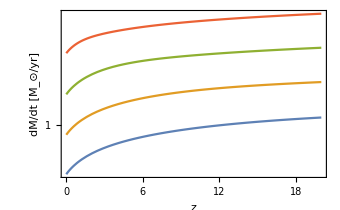

```mathematica
Plot[10^-6*dotMi[z,10^#]&/@Range[8,14,2]//Log10//Evaluate,{z,dotMi[[1,1,1]],20},FrameLabel->{"z","dM/dt ["<>Msunt<>"/yr]"},FrameTicks->{{logticksx,logticksx2},Automatic},ImageSize->340]
```

```mathematica
find0[X_]:=Module[{Xmax,jcut},
Xmax = First@First@MaximalBy[X,Last];
jcut = First@Flatten@Position[Select[X,#[[1]]>Xmax&],0];
X[[1;;jcut]]
]
Plnmulist = ReadList[NotebookDirectory[]<>"Plnmu.dat",Table[Number,{3}]];
zlist = DeleteDuplicates[Plnmulist[[All,1]]]
Plnmulist =GatherBy[Plnmulist,First][[All,All,{2,3}]];
Plnmui = Interpolation[find0[#],InterpolationOrder->1]&/@Plnmulist;
Plnmuf=Table[Function[lnmu,Piecewise[{{Plnmui[[j]][lnmu],Plnmui[[j]][[1,1,1]]<lnmu < Plnmui[[j]][[1,1,2]]}},0]//Evaluate],{j,Length@Plnmui}];
```

{4,5,6,7,8,9,10,11,12.5,14.5}

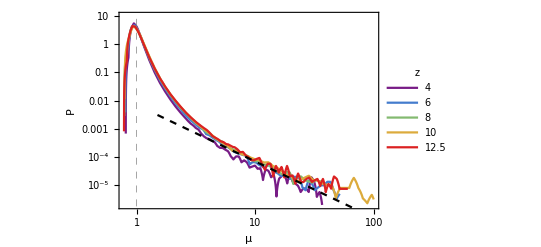

```mathematica
Show[LogLogPlot[#[Log@x]&/@Plnmuf[[1;;-1;;2]]//Evaluate,{x,0.7,100},PlotRange->{All,{2.*^-6,10}},GridLines->{{1},{}},GridLinesStyle->Directive[Gray, Dashed],FrameLabel->{"μ","P"},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,4]),PlotLegends->LineLegend[Automatic,zlist[[1;;-1;;2]],LegendMarkerSize->{10,4},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendLabel->Style["z",14]]],
LogLogPlot[0.007x^-2,{x,1.5,100},PlotStyle->Directive[Black,Dashed]]]
```

```mathematica
data1 = Import[NotebookDirectory[]<>"UVLF_2102.07775.txt","Table"];
DeleteDuplicates[data1[[All,1]]]
Φ1[z_]:=Select[data1,#[[1]]==z&][[All,2;;5]]
data2 = Import[NotebookDirectory[]<>"UVLF_2108.01090.txt","Table"];
DeleteDuplicates[data2[[All,1]]]
Φ2[z_]:=Select[data2,#[[1]]==z&][[All,2;;5]]
data3 = Import[NotebookDirectory[]<>"UVLF_2403.03171.txt","Table"];
DeleteDuplicates[data3[[All,1]]]
Φ3[z_]:=Select[data3,#[[1]]==z&][[All,2;;5]]
```

{4,5,6,7,8,9,10}

{4,5,6,7}

{9,10,11,12.5,14.5}

```mathematica
UVL = ReadList[NotebookDirectory[]<>"UVluminosity.dat",Table[Number,{5}]];
zlist = UVL[[All,1]]//DeleteDuplicates
UVL = GatherBy[UVL,First][[All,All,2;;-1]];
UVLi = Table[Interpolation[UVL[[j,All,{1,4}]],InterpolationOrder->1],{j,Length@UVL}];
```

{4,5,6,7,8,9,10,11,12.5,14.5}

```mathematica
NPDF2[x_,μ_,σm_,σp_]:= 2Piecewise[{{σm PDF[NormalDistribution[μ,σm],x],x<μ}},σp PDF[NormalDistribution[μ,σp],x]]/(σm+σp)
Total@Flatten@Table[Log@NPDF2[10^9UVLi[[jz]][#[[1]]],#[[2]],#[[3]],#[[4]]]&/@Join[Φ1[zlist[[jz]]],Φ2[zlist[[jz]]],Φ3[zlist[[jz]]]],{jz,Length@zlist}]
```

1415.38

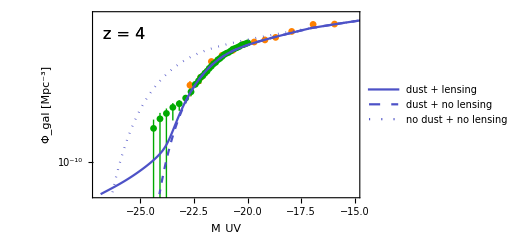

```mathematica
jz0 = 1;
Legended[Show[ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ1[zlist[[jz0]]]//Evaluate,PlotStyle->Orange,PlotRange->{{-27,-15},{-12,-1}},FrameLabel->{"M_UV","Φ_gal [Mpc^-3]"},FrameTicks->{{logticksx,logticksx2},Automatic},PlotStyle->DotDashed,ImageSize->380],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ2[zlist[[jz0]]]//Evaluate,PlotStyle->Darker@Green],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ3[zlist[[jz0]]]//Evaluate,PlotStyle->Darker@Cyan],
Graphics[Text[Style["z = "<>ToString@zlist[[jz0]],16],Scaled@{0.12,0.88}]],
ListPlot[{{#[[1]],Log10[10^9#[[2]]]}&/@UVL[[jz0]],{#[[1]],Log10[10^9#[[3]]]}&/@UVL[[jz0]],{#[[1]],Log10[10^9#[[4]]]}&/@UVL[[jz0]]}//Evaluate,PlotRange->{{-27,-15},{-12,-1}},Joined->True,PlotStyle->{Directive[RGBColor[0.3,0.32,0.78],Dotted],Directive[RGBColor[0.3,0.32,0.78],Dashed],Directive[RGBColor[0.3,0.32,0.78]]}],
Graphics[Text[Style["z = "<>ToString@zlist[[jz0]],16],Scaled@{0.12,0.88}]]],Placed[LineLegend[{RGBColor[0.3,0.32,0.78],Directive[RGBColor[0.3,0.32,0.78],Dashed],Directive[RGBColor[0.3,0.32,0.78],Dotted]},{"dust + lensing","dust + no lensing","no dust + no lensing"},LabelStyle->{FontSize->14,FontFamily->"Times"},LegendMarkerSize->{24,4}],Scaled@{0.72,0.25}]]
```

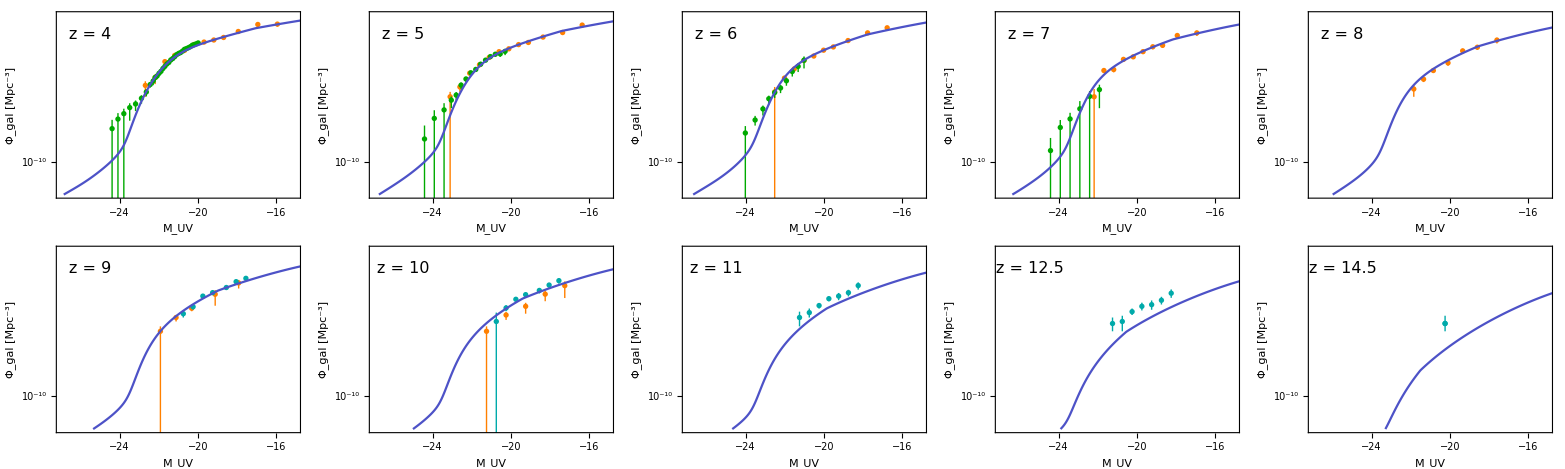

```mathematica
Grid@ArrayReshape[Table[Show[ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ1[zlist[[jz0]]]//Evaluate,PlotStyle->Orange,PlotRange->{{-27,-15},{-12,-1}},FrameLabel->{"M_UV","Φ_gal [Mpc^-3]"},FrameTicks->{{logticksx,logticksx2},Automatic},PlotStyle->DotDashed,ImageSize->300],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ2[zlist[[jz0]]]//Evaluate,PlotStyle->Darker@Green],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ3[zlist[[jz0]]]//Evaluate,PlotStyle->Darker@Cyan],
ListPlot[{#[[1]],Log10[10^9#[[4]]]}&/@UVL[[jz0]]//Evaluate,PlotRange->{{-27,-15},{-12,-1}},Joined->True,PlotStyle->Directive[RGBColor[0.3,0.32,0.78]]],
Graphics[Text[Style["z = "<>ToString@zlist[[jz0]],16],Scaled@{0.14,0.88}]]],{jz0,Length@zlist}],{2,5}]
```

```mathematica
MCMCchain = ReadList[NotebookDirectory[]<>"MCMCchains.dat",Table[Number,{5}]];
MCMCchain[[All,1]] = MCMCchain[[All,1]]/10^11;
Length@MCMCchain
```

2850

{1.98881,0.0748217,-0.943387,0.304319,1401.48}

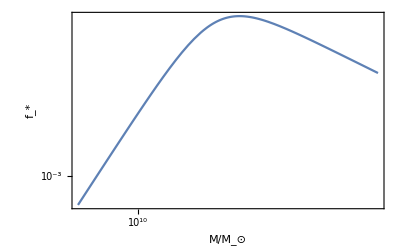

```mathematica
fstar[M_,Mc_,ϵ_,α_,β_]:=ϵ/((M/Mc)^α+(M/Mc)^β)
First@MaximalBy[MCMCchain,Last]
Plot[Log10@fstar[10^logM,%[[1]]*10^11,%[[2]],%[[3]],%[[4]]],{logM,9,14},FrameTicks->{{logticksx,logticksx2},{logticksx,logticksx2}},PlotRange->{All,{All,-1}},FrameLabel->{"M/"<>Msunt,"f_*"}]
```

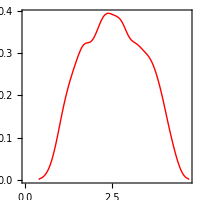
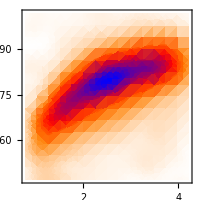
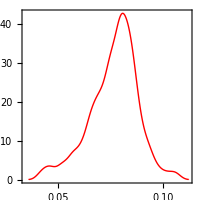
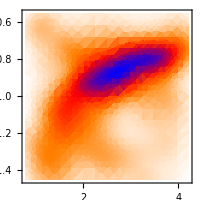
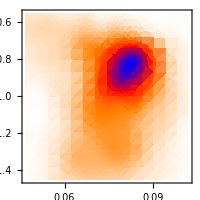
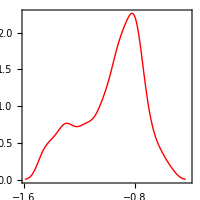
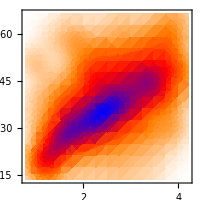
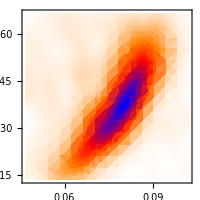
-Graphics- |  |  | 
-Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
CP[i_,j_]:=SmoothDensityHistogram[MCMCchain[[All,{j,i}]],ImageSize->200,ImagePadding->{{40,4},{40,4}},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.004]],BaseStyle->{FontSize->14,FontFamily->"Times"},ColorFunction->(Blend[{White,Orange,Red,Purple,Blue},#]&),MeshFunctions->{#3&},MeshStyle->Directive[White,Dashed],Mesh->2]
CP[i_]:=SmoothHistogram[MCMCchain[[All,i]],ImageSize->200,ImagePadding->{{40,4},{40,4}},AspectRatio->1,Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],BaseStyle->{FontSize->14,FontFamily->"Times"},PlotStyle->Directive[Red,Thick]]
Grid[Table[If[i>j,CP[i,j],If[i==j,CP[i]]],{i,1,4},{j,1,4}]]
```